```mathematica
Get[StringJoin[NotebookDirectory[],"PlaneCurvePlot.wl"]]
```

## Pedal

#### (* Pedal of a circle is the Limacon of Pascal *)

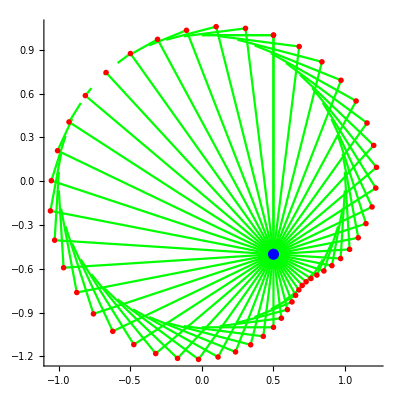

```mathematica
PlaneCurvePlot[{Sin[t],Cos[t]},{t,0,2 π,(2 π)/50},PedalPoint->{.5,-.5},PlotCurve->False,PlotDot->False,AspectRatio->Automatic]
```

#### (* Pedal of astroid with respect to its center is 4 leaved rose *)

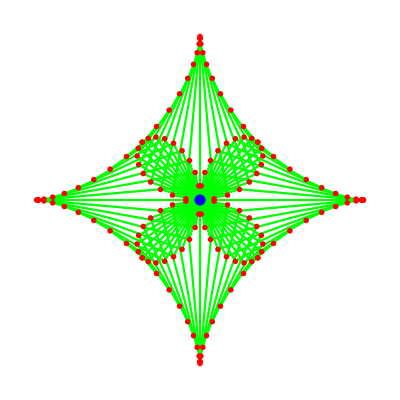

```mathematica
PlaneCurvePlot[{(3 Cos[t])/4+1/4 Cos[3 t],(3 Sin[t])/4-1/4 Sin[3 t]},{t,0,2 π,(2 π)/(4 18)},PlotCurve->False,PedalPoint->{0,0},Axes->False,AspectRatio->Automatic]
```

#### (* Pedal of a hyperbola with respect to its focus is a circle *)

```mathematica
PlaneCurvePlot[{-Sec[t],Tan[t]},{t,-1.2,1.2},Range[-1.5,1.5,.1],PedalPoint->{1.5,0},PlotDot->False,CurveColorFunction->{Hue[0]&},AspectRatio->Automatic,PlotRange->{{-2.4,1.8},{-2,2}}]
```

-Graphics-

#### (* Pedal of a hyperbola with respect to its center is lemniscate of Bernoulli *)

```mathematica
PlaneCurvePlot[{-Sec[t],Tan[t]},{t,-1.2,1.2},Range[-1.5,1.5,.1],PedalPoint->{0,0},PlotDot->False,CurveColorFunction->{Hue[0]&},AspectRatio->Automatic,PlotRange->{{-2,.05},{-1.5,1.5}}]
```

-Graphics-

#### (* Pedal of Parabola with respect to its focus is a line *)

```mathematica
PlaneCurvePlot[{t,t^2/2},{t,-2,2,.2},PedalPoint->{0,1/2},PlotDot->False,DotStyle->{{Hue[0],PointSize[.02]}},LineStyle->{Hue[0]},CurveStyle->{Thickness[.008]},AspectRatio->Automatic,PlotRange->{{-1.2,1.2},{-.2,.8}},Axes->True]
```

-Graphics-

#### (* Pedal of an ellipse with respect to its focus is a circle *)

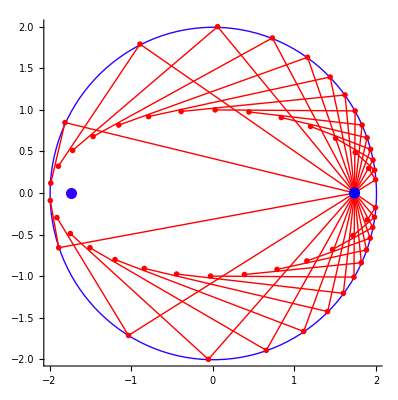

```mathematica
PlaneCurvePlot[{2 Cos[t],1 Sin[t]},{t,0,2 π},Range[0.3,6,(2 π)/30],PedalPoint->{1.737,0},PlotDot->True,LineStyle->{Hue[0]},PlotCurve->False,PlotRange->All,AspectRatio->Automatic,Prolog->{Hue[0.7],PointSize[.02],Point[{-1.737,0}],Hue[0.7],Circle[{0,0},2]}]
```

#### (* Hypotrochoid beauty. [1,2/3,.4] *)

```mathematica
PlaneCurvePlot[{0.4 Cos[t/2]+Cos[t]/3,-0.4 Sin[t/2]+Sin[t]/3},{t,0,2 2 π,(2 2 π)/(5 18)},PedalPoint->{0,0},Axes->False,PlotDot->False,AspectRatio->Automatic]
```

-Graphics-

#### (* Hypotrochoid beauty, [1, 3/4, .5] *)

```mathematica
PlaneCurvePlot[{0.5 Cos[t/3]+Cos[t]/4,-0.5 Sin[t/3]+Sin[t]/4},{t,0,3 2 π,(3 2 π)/(4 20)},PedalPoint->{0,0},Axes->False,PlotDot->False,LineStyle->{Hue[Random[]]},AspectRatio->Automatic]
```

-Graphics-